## General setup

### Metric setup

#### Load up Steve’s GR & tensor libraries

```mathematica
SetDirectory[NotebookDirectory[]];
<<GRtensors
```

#### Set the metric for the example from Section 4.1. of Chesler & Yaffe’s review 1309.1439

```mathematica
ggValues={{-2A[t,r],0,0,0,1},{0,Σ[t,r]^2*Exp[B[t,r]],0,0,0},{0,0,Σ[t,r]^2*Exp[B[t,r]],0,0},{0,0,0,Σ[t,r]^2*Exp[-2B[t,r]],0},{1,0,0,0,0}};
ggiValues=Inverse[ggValues];
SetXMet[{t,x1,x2,x3,r},ggValues,ggiValues];
DisplayTensor[gg]//MatrixForm
```

(-2 A[t,r] | 0 | 0 | 0 | 1
0 | ⅇ^B[t,r] Σ[t,r]^2 | 0 | 0 | 0
0 | 0 | ⅇ^B[t,r] Σ[t,r]^2 | 0 | 0
0 | 0 | 0 | ⅇ^(-2 B[t,r]) Σ[t,r]^2 | 0
1 | 0 | 0 | 0 | 0)

#### Generate all the relevant GR tensors

```mathematica
NewTensor[chris, chrisDef, Simplify];
NewTensor[chrisCont,chrisContDef, Simplify];
NewTensor[ricci,QuickRicciDef, Simplify];
NewTensor[einstein,einsteinDef, Simplify];
scalarR = Simplify[ComputeScalarR];
```

#### Bulk stress for empty AdS

```mathematica
StressDef[DefaultIndexType]={DownVector,DownVector};
StressDef[{m_,n_}]:=-Λ*gg[{{m,DownVector},{n,DownVector}}];
NewTensor[Stress,StressDef,Simplify]
```

#### Null

```mathematica
ΛRule={Λ->-1/2*Dim*(Dim-1)*1/L^2};
```

#### Compute Einstein equations

```mathematica
EinsteinEqs = DisplayTensor[einstein,{DownVector,DownVector}]-DisplayTensor[Stress,{DownVector,DownVector}]/.ΛRule/.Dim->4/.L->1//Simplify;
```

### Nested equations of motion

#### Null

```mathematica
NonZeroComp={};
Do[If[ToString[EinsteinEqs[[mu,nu]]]≠"0",NonZeroComp=Append[NonZeroComp,{mu,nu}]],{mu,1,dim},{nu,1,dim}]
NonZeroComp
```

{{1,1},{1,5},{2,2},{3,3},{4,4},{5,1},{5,5}}

#### Check that EoMs (2,2) and (3,3) are the same, as well as (1,5) and (5,1)

```mathematica
ShouldBeZero=EinsteinEqs[[2,2]]-EinsteinEqs[[3,3]]
```

0

```mathematica
ShouldBeZero=EinsteinEqs[[1,5]]-EinsteinEqs[[5,1]]
```

0

#### Rules for replacing temporal derivatives ∂_t with the “null” derivatives d_+:

```mathematica
dpRules={
Derivative[1,0][Σ][t,r]->dpΣ[t,r]-A[t,r]*Derivative[0,1][Σ][t,r],
Derivative[1,0][B][t,r]->dpB[t,r]-A[t,r]*Derivative[0,1][B][t,r],
Derivative[1,0][A][t,r]->dpA[t,r]-A[t,r]*Derivative[0,1][A][t,r],
Derivative[1,1][Σ][t,r]->Derivative[0,1][dpΣ][t,r]-A[t,r]*Derivative[0,2][Σ][t,r]-Derivative[0,1][A][t,r]*Derivative[0,1][Σ][t,r],
Derivative[1,1][A][t,r]->Derivative[0,1][dpA][t,r]-A[t,r]*Derivative[0,2][A][t,r]-Derivative[0,1][A][t,r]*Derivative[0,1][A][t,r],
Derivative[1,1][B][t,r]->Derivative[0,1][dpB][t,r]-A[t,r]*Derivative[0,2][B][t,r]-Derivative[0,1][A][t,r]*Derivative[0,1][B][t,r],
Derivative[2,0][Σ][t,r]->dpdpΣ[t,r]-dpA[t,r]*Derivative[0,1][Σ][t,r]-2A[t,r]*Derivative[0,1][dpΣ][t,r]+2*A[t,r]*Derivative[0,1][A][t,r]*Derivative[0,1][Σ][t,r]+A[t,r]^2*Derivative[0,2][Σ][t,r]
};
```

#### Null

```mathematica
RelevantComponents={{1,1},{1,5},{2,2},{4,4},{5,5}};
```

```mathematica
EERelevant=Table[EinsteinEqs[[i[[1]],i[[2]]]]/.dpRules//Simplify,{i,RelevantComponents}];
```

#### Null

```mathematica
OverallFactors={2/3 Σ[t,r]^2,2/3 Σ[t,r]^2,2*ⅇ^(-B[t,r]),2*ⅇ^(2B[t,r]),-1/3*Σ[t,r]};
```

```mathematica
EESimplified=EERelevant*OverallFactors//Simplify;
```

#### Null

```mathematica
NestCoeff={{0,0,0,0,1},{0,1/(2Σ[t,r]),0,0,-A[t,r]},{0,0,-1/(6 Σ[t,r]),1/(6 Σ[t,r]),0},{0,-2/Σ[t,r]^2,1/(3 Σ[t,r]^2),1/(6 Σ[t,r]^2),(4A[t,r])/Σ[t,r]}};
```

```mathematica
EoMNested=NestCoeff.EESimplified//Simplify;
```

#### Null

```mathematica
EoMNested//MatrixForm
```

(1/2 Σ[t,r] (B^(0,1)[t,r])^2+Σ^(0,2)[t,r]
-2 Σ[t,r]+dpΣ^(0,1)[t,r]+(2 dpΣ[t,r] Σ^(0,1)[t,r])/Σ[t,r]
3/2 dpΣ[t,r] B^(0,1)[t,r]+Σ[t,r] dpB^(0,1)[t,r]+3/2 dpB[t,r] Σ^(0,1)[t,r]
2+3/2 dpB[t,r] B^(0,1)[t,r]-(6 dpΣ[t,r] Σ^(0,1)[t,r])/Σ[t,r]^2+A^(0,2)[t,r])

#### Starting from knowing B at some time t0, - integrate the first equation to get Σ(t0,r) - integrate the second equation to get d+Σ(t0,r) - integrate the third equation to get d+B(t0,r) - integrate the fourth equation to get A(t0,r)

### Field redefinitions and change of coordinates

#### Null

```mathematica
InvRadRules={
Σ->Function[{t,u},Σ[t,1/u]],dpΣ->Function[{t,u},dpΣ[t,1/u]],
B->Function[{t,u},B[t,1/u]],dpB->Function[{t,u},dpB[t,1/u]],
A->Function[{t,u},A[t,1/u]]
};
```

```mathematica
EoMInverted=EoMNested/.r->1/u/.InvRadRules//Simplify;
```

#### Null

```mathematica
Redefinitions={
Σ->Function[{t,u},1/u+λ[t]+u^4*σ[t,u]],
dpΣ->Function[{t,u},u^2*σDot[t,u]+1/2(1/u+λ[t])^2],
A->Function[{t,u},a[t,u]+1/2*(1/u+λ[t])^2],
B->Function[{t,u},b[t,u]*u^3],
dpB->Function[{t,u},bDot[t,u]*u^3]
};
```

#### Null

#### Null

#### Null

```mathematica
EoMFacs={2*u^-6,(1+u λ[t]+u^5 σ[t,u])u^-4,4 u^-2,2/u^3 (1+u λ[t]+u^5 σ[t,u])^2};
```

```mathematica
EoMFinal=Expand[EoMFacs*EoMInverted/.Redefinitions]//Simplify;
```

#### Null

```mathematica
EoMFinal/.u->0
```

{40 σ[t,0],-7 σ[t,0]-2 λ[t] σDot[t,0]-σDot^(0,1)[t,0],-9 b[t,0],4 a^(0,1)[t,0]}

### Horizon stationarity condition

```mathematica
HorizonStatCondFull=dpdpΣ[t,r]-A[t,r] Derivative[0,1][dpΣ][t,r];
```

```mathematica
dpdpΣSol=Solve[EESimplified[[1]]==0,dpdpΣ[t,r]][[1]];
```

```mathematica
drdrΣSol=Solve[EoMNested[[1]]==0,Derivative[0,2][Σ][t,r]][[1]];
```

```mathematica
drdpΣSol=Solve[EoMNested[[2]]==0,Derivative[0,1][dpΣ][t,r]][[1]];
```

## Module definitions

### Pseudospectral discretization

```mathematica
PseudoDiscretization[uMinLocal_,uMaxLocal_,NumPointsLocal_]:=Module[{uMin=uMinLocal,uMax=uMaxLocal,NumPoints=NumPointsLocal},
xj=Table[Cos[(π*(i-1))/NumPoints],{i,1,NumPoints+1}]//N;
uj=uMin+(uMax-uMin)/2(1+xj);
pj=Table[If[(j==1)||(j==NumPoints+1),2,1],{j,1,NumPoints+1}];
δij=IdentityMatrix[NumPoints+1];
δij[[1,1]]=(1+2 NumPoints^2)/6;
δij[[NumPoints+1,NumPoints+1]]=-(1+2 NumPoints^2)/6;
Do[δij[[j,j]]=(-xj[[j]])/(2(1-xj[[j]]^2)),{j,2,NumPoints}];Do[If[i≠j,δij[[i,j]]=(-1)^(i+j)*pj[[i]]/(pj[[j]]*(xj[[i]]-xj[[j]]))],{i,1,NumPoints+1},{j,1,NumPoints+1}];
DMat=2/(uMax-uMin)*δij;
{bVec,bDotVec,σVec,σDotVec,aVec}=
Transpose[Table[{bj[j][t],bDotj[j][t],σj[j][t],σDotj[j][t],aj[j][t]},{j,1,NumPoints+1}]];
dbVec=DMat.bVec;
dbDotVec=DMat.bDotVec;
dσVec=DMat.σVec;
ddσVec=DMat.DMat.σVec;
dσDotVec=DMat.σDotVec;
daVec=DMat.aVec;
ddaVec=DMat.DMat.aVec;
DiscreteRules[i_]:={
b[t,u]->bj[i][t],bDot[t,u]->bDotj[i][t],
σ[t,u]->σj[i][t],σDot[t,u]->σDotj[i][t],
a[t,u]->aj[i][t],
Derivative[0,1][b][t,u]->dbVec[[i]],Derivative[0,1][bDot][t,u]->dbDotVec[[i]],
Derivative[0,1][σ][t,u]->dσVec[[i]],Derivative[0,2][σ][t,u]->ddσVec[[i]],Derivative[0,1][σDot][t,u]->dσDotVec[[i]],
Derivative[0,1][a][t,u]->daVec[[i]],Derivative[0,2][a][t,u]->ddaVec[[i]]
};
Do[EoMDiscrete[j]=Table[EoMFinal[[j]]/.DiscreteRules[i]/.u->uj[[i]],{i,1,NumPoints+1}],{j,1,4}];
xRule=Solve[uSym==uMin+(uMax-uMin)/2(1+xSym),xSym][[1]];
bInitj=Table[bInit[uj[[j]]],{j,1,NumPoints+1}];
bInitRules=Table[bj[j][t0]->bInitj[[j]],{j,1,NumPoints+1}];
];
```

### Generate initial conditions

```mathematica
GenerateIC[PolyOrderLocal_,MySeedLocal_,bAmplLocal_]:=Module[{PolyOrder=PolyOrderLocal,MySeed=MySeedLocal,bAmpl=bAmplLocal},
SeedRandom[MySeed];
CoeffUp=RandomReal[{0,1},PolyOrder+1];
CoeffDown=RandomReal[{0,1},PolyOrder+1];
CoeffUpRules=Table[cUp[i-1]->CoeffUp[[i]],{i,1,Length[CoeffUp]}];

CoeffDownRules=Table[cDown[i-1]->CoeffDown[[i]],{i,1,Length[CoeffDown]}];
bICTrial[u_]=(Sum[cUp[i] u^i,{i,0,10}]/.CoeffUpRules)/(Sum[cDown[i] u^i,{i,0,10}]/.CoeffDownRules);
ConstTerm=SeriesCoefficient[bICTrial[u],{u,0,0}];
bIC[u_]=bAmpl*(bICTrial[u]-ConstTerm);
a4IC=-1/2;
λInitRule={λ[t0]->0};
a4Rule={a4->a4IC};
bInit[u_]:=bIC[u];
];
```

### Chebyshev interpolation

```mathematica
ChebyshevInt[FunctionNameLocal_,FunctionValuesLocal_]:=Module[{FunctionName=FunctionNameLocal,FunctionValues=FunctionValuesLocal},
fTemp[u_]=Sum[α[n]*ChebyshevT[n-1,xSym/.xRule],{n,1,NumPoints+1}]/.uSym->u;
CoeffRules=Solve[Table[fTemp[uj[[j]]]==FunctionValues[[j]],{j,1,NumPoints+1}],Table[α[n],{n,1,NumPoints+1}]][[1]];
ToExpression [FunctionName][u_]=fTemp[u]/.CoeffRules;
];
```

### Solving EoMs initially

```mathematica
SolveEoM1Initially:=Module[{},
σBCInitRule={σj[NumPoints+1][t0]->0};
EoMD1Init=EoMDiscrete[1]/.t->t0/.bInitRules/.σBCInitRule/.λInitRule;
σSolInitRules=NSolve[Table[EoMD1Init[[j]]==0,{j,1,NumPoints}],σVec[[1;;NumPoints]]/.t->t0];
σSolInitRules=Join[σSolInitRules[[1]],σBCInitRule];
];
```

```mathematica
SolveEoM2Initially:=Module[{},
σDotBCInitRule ={σDotj[NumPoints+1][t0]->a4};
EoMD2Init=EoMDiscrete[2]/.t->t0/.σSolInitRules/.σDotBCInitRule/.λInitRule/.a4Rule;σDotSolInitRules=NSolve[Table[EoMD2Init[[j]]==0,{j,1,NumPoints}],σDotVec[[1;;NumPoints]]/.t->t0];
σDotSolInitRules=Join[σDotSolInitRules[[1]],σDotBCInitRule/.a4Rule];
];
```

## Specifying family of initial conditions

### Generate random backgrounds

```mathematica
HowManyBkgs=70;
```

#### Randomly generate seeds of varying size

```mathematica
SeedList={};
Do[
Pwr=RandomInteger[{2,7}];
SeedList=Append[SeedList,RandomInteger[{1,10^Pwr}]];
,{i,1,HowManyBkgs}]
```

#### This is the seed list I chose

```mathematica
SeedList={8721,1179,319,384348,5544,3048,8371,70960,63863,98502,46574,566,33699,723227,82278,96938,8909259,6741653,414,73,58391,24221,1586,518,4398,5610422,3731271,230,54,154883,5936,30713,645113,610,954568,87,113,682,3857,51,937539,8140,3829,92261,48,16714,65789,142265,4384,4396,307,86291,292768,7761954,4491,88,4806,80518,6187,771214,747,1,99,948,952556,53,80,6853,8976,36935};
```

#### Use it to generate the backgrounds

```mathematica
MyBkgs={};
Do[
GenerateIC[10,SeedList[[i]],1];
MyBkgs=Append[MyBkgs,bIC[u]];
,{i,1,HowManyBkgs}]
```

#### Identify the backgrounds that are too extreme and get rid of them

```mathematica
ExtremeBkgs={};
Do[
If[Abs[MyBkgs[[i]]/.u->0.9]>2,ExtremeBkgs=Append[ExtremeBkgs,{i}]];
,{i,1,HowManyBkgs}]
```

```mathematica
MyBkgs=Delete[MyBkgs,ExtremeBkgs];
```

#### Plot the remaining bkgs

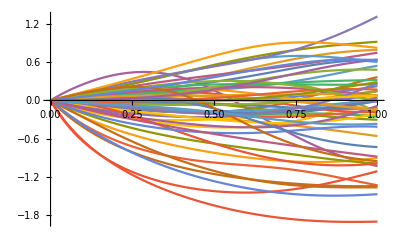

```mathematica
Plot[MyBkgs,{u,0,1},PlotRange->All]
```

#### Check that this is linear close to u = 0

```mathematica
ConstTerms=Table[SeriesCoefficient[MyBkgs[[i]],{u,0,0}],{i,1,Length[MyBkgs]}];
AllTrue[ConstTerms,#<10^-3&]
```

True

### Modified IC generator

```mathematica
GenerateICMod[PolyOrderLocal_,iLocal_,bAmplLocal_]:=Module[{PolyOrder=PolyOrderLocal,ii=iLocal,bAmpl=bAmplLocal},
bIC[uu_]=bAmpl*MyBkgs[[ii]]/.u->uu;
(*bIC[u_]=bAmpl*(bICTrial[u]-ConstTerm);*)
a4IC=-1/2;
λInitRule={λ[t0]->0};
a4Rule={a4->a4IC};
bInit[u_]:=bIC[u];
];
```

## Finding initial apparent horizon

### Initial conditions

```mathematica
MyAmplitude=1;
MyUMax=1.5;
WhichBkg=1;
```

### Step by step code for debugging

#### Set the initial conditions

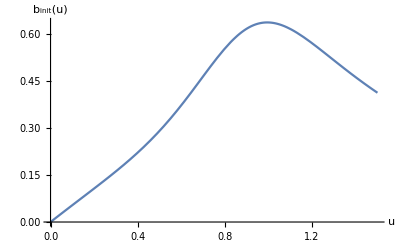

```mathematica
ThereIsAHorizon=False;
GenerateICMod[10,WhichBkg,MyAmplitude];
NumPoints=25;
uMin=0;
uMax=MyUMax;
Plot[bInit[u],{u,uMin,uMax},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"u","b_init(u)"}]
```

#### Solve the first nested EoM

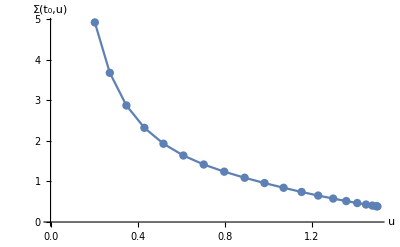

```mathematica
PseudoDiscretization[uMin,uMax,NumPoints];
SolveEoM1Initially;
ΣInitList=Table[{uj[[i]],Σ[t,u]/.Redefinitions/.DiscreteRules[i]/.u->uj[[i]]/.t->t0/.λInitRule/.σSolInitRules},{i,1,NumPoints}];
GetRidOfPoints=6;
ListPlot[ΣInitList[[;;-GetRidOfPoints]],Joined->True,AxesOrigin->{0,0},AxesLabel->{"u","Σ(t_0,u)"},PlotRange->All,Mesh->Full]
```

#### If there is a caustic, reduce the region in u

```mathematica
IsΣPositive=Min[ΣInitList[[;;,2]]]>0;
WasΣPositive=IsΣPositive;
If[IsΣPositive==False,{
Do[If[ΣInitList[[i,2]]≤0,{uMaxNew=ΣInitList[[i+2,1]];Break[];}],{i,Length[ΣInitList],1,-1}];
uMax=uMaxNew;
PseudoDiscretization[uMin,uMax,NumPoints];
SolveEoM1Initially;
IsΣPositive=True;
}];
uMaxNew
```

uMaxNew

#### Solve the second nested equation

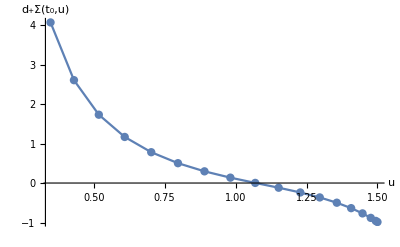

```mathematica
SolveEoM2Initially;
dpΣInitList=Table[{uj[[i]],dpΣ[t,u]/.Redefinitions/.DiscreteRules[i]/.u->uj[[i]]/.t->t0/.λInitRule/.σDotSolInitRules},{i,1,NumPoints}];
GetRidOfPoints=8;
ListPlot[dpΣInitList[[1;;-GetRidOfPoints]],AxesLabel->{"u","d_+Σ(t_0,u)"},Joined->True,Mesh->Full]
```

#### Check if there is an apparent horizon

```mathematica
dpΣFirstNegative=dpΣInitList[[1,2]]<0;
dpΣNegative=dpΣFirstNegative;
Cnt=2;
While[dpΣNegative&&Cnt≤NumPoints,{
dpΣNegative=dpΣInitList[[Cnt,2]]<0;
Cnt=Cnt+1;
}];
FirstHalfdpΣPositive=Min[dpΣInitList[[Cnt-1;;NumPoints,2]]]>0;
SecondHalfdpΣNegative=Max[dpΣInitList[[1;;Cnt-2,2]]]<0;
If[dpΣFirstNegative==True,
{If[FirstHalfdpΣPositive&&SecondHalfdpΣNegative,ThereIsAHorizon=True;,ThereIsAHorizon=False;];},
{ThereIsAHorizon=False;}
];
ThereIsAHorizon
```

True

#### If there is a horizon find it by truncating the search region just outside it, and increasing the number of collocation points to 50

```mathematica
If[ThereIsAHorizon,{
uMax=dpΣInitList[[Cnt-2,1]];
NumPoints=50;
PseudoDiscretization[uMin,uMax,NumPoints];
SolveEoM1Initially;
SolveEoM2Initially;
ChebyshevInt["σDotAnal",Table[σDotj[j][t0]/.σDotSolInitRules,{j,1,NumPoints+1}]];
dpΣAnal[u_]=dpΣ[t,u]/.Redefinitions/.t->t0/.λInitRule/.σDot[t0,u]-> σDotAnal[u];
uHorizonInit=u/.FindRoot[dpΣAnal[u]==0,{u,0.99uMax}];
}];
uHorizonInit
```

1.07144

#### If there is no horizon, we have two options: 1.) If there was no caustic (and hence we didn’t shrink the u-region before), extend the region and repeat everything again 2.) If there was a caustic (and we had to shrink the u-region), then we cannot solve these IC, and an option is to start decreasing the amplitude of b

```mathematica
If[ThereIsAHorizon==False&&WasΣPositive==True,{
MyUMax=MyUMax+0.1;
}];
If[ThereIsAHorizon==False&&WasΣPositive==False,{
MyAmplitude=0.9*MyAmplitude;
}];
MyUMax
MyAmplitude
```

1.5

1

### Full automatization for one IC

```mathematica
FindHorizon[MyILocal_,MyAmplitudeLocal_,MyUMaxLocal_]:=Module[{MyI=MyILocal,MyAmplitude=MyAmplitudeLocal,MyUMax=MyUMaxLocal},
LogString="Starting with bkg = "<>ToString[MyI]<>", A_b = "<>ToString[MyAmplitude] <>" and u_max = "<>ToString[MyUMax]<>"\n----------\n";
MainCnt=1;
ThereIsAHorizon=False;
While[ThereIsAHorizon==False,
(* Generate IC and discretize *)
NumPoints=25;
uMin=0;
uMax=MyUMax;
GenerateICMod[10,MyI,MyAmplitude];
PseudoDiscretization[uMin,uMax,NumPoints];

(* Solve the first nested EoM *)
SolveEoM1Initially;
ΣInitList=Table[{uj[[i]],Σ[t,u]/.Redefinitions/.DiscreteRules[i]/.u->uj[[i]]/.t->t0/.λInitRule/.σSolInitRules},{i,1,NumPoints}];

(* If there is a caustic, reduce the region in u *)
IsΣPositive=Min[ΣInitList[[;;,2]]]>0;
WasΣPositive=IsΣPositive;
If[IsΣPositive==False,{
Do[If[ΣInitList[[i,2]]≤0,{uMaxNew=ΣInitList[[i+2,1]];Break[];}],{i,Length[ΣInitList],1,-1}];
uMax=uMaxNew;
PseudoDiscretization[uMin,uMax,NumPoints];
SolveEoM1Initially;
IsΣPositive=True;
}];

(* Solve the second nested equation *)
SolveEoM2Initially;
dpΣInitList=Table[{uj[[i]],dpΣ[t,u]/.Redefinitions/.DiscreteRules[i]/.u->uj[[i]]/.t->t0/.λInitRule/.σDotSolInitRules},{i,1,NumPoints}];

(* Check if there is an apparent horizon *)
dpΣFirstNegative=dpΣInitList[[1,2]]<0;
dpΣNegative=dpΣFirstNegative;
Cnt=2;
While[dpΣNegative&&Cnt≤NumPoints,{
dpΣNegative=dpΣInitList[[Cnt,2]]<0;
Cnt=Cnt+1;
}];
FirstHalfdpΣPositive=Min[dpΣInitList[[Cnt-1;;NumPoints,2]]]>0;
SecondHalfdpΣNegative=Max[dpΣInitList[[1;;Cnt-2,2]]]<0;
If[dpΣFirstNegative==True,
If[FirstHalfdpΣPositive&&SecondHalfdpΣNegative,ThereIsAHorizon=True;,ThereIsAHorizon=False;];,
ThereIsAHorizon=False;
];

(* If there is a horizon, find it *)
If[ThereIsAHorizon==True,{
LogString=LogString<>"----------\nFound horizon at ...";
uMax=dpΣInitList[[Cnt-2,1]];
NumPoints=50;
PseudoDiscretization[uMin,uMax,NumPoints];
SolveEoM1Initially;
SolveEoM2Initially;
ChebyshevInt["σDotAnal",Table[σDotj[j][t0]/.σDotSolInitRules,{j,1,NumPoints+1}]];
dpΣAnal[u_]=dpΣ[t,u]/.Redefinitions/.t->t0/.λInitRule/.σDot[t0,u]-> σDotAnal[u];
uHorizonInit=u/.FindRoot[dpΣAnal[u]==0,{u,0.99uMax}];
LogString=LogString<>" u_horizon = "<>ToString[uHorizonInit];
}];

(* If there was no horizon and there was no caustic, extend the u-region *)
If[ThereIsAHorizon==False&&WasΣPositive==True,{
MyUMax=MyUMax+0.1;
LogString=LogString<>ToString[MainCnt]<>".) No horizon and no caustic, extending u_max to "<>ToString[MyUMax]<>"\n";
}];

(* If there was no horizon and there was a caustic, reduce the amplitude of b *)
If[ThereIsAHorizon==False&&WasΣPositive==False,{
MyAmplitude=0.9*MyAmplitude;
LogString=LogString<>ToString[MainCnt]<>".) No horizon, but caustic observed, reducing A_b to "<>ToString[MyAmplitude]<>"\n";
}];

MainCnt=MainCnt+1;
]];
```

### Run it and monitor output

```mathematica
FindHorizon[1,MyAmplitude,MyUMax]
```

```mathematica
Dynamic[LogString]
```

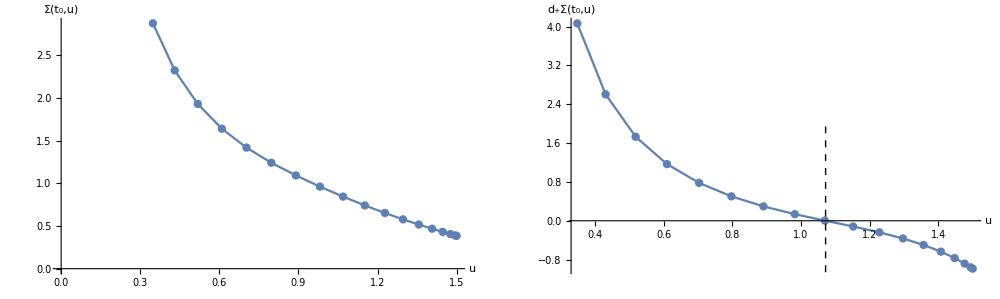

```mathematica
GetRidOfPoints=8;
ΣInitPlot=ListPlot[ΣInitList[[1;;-GetRidOfPoints]],Joined->True,AxesOrigin->{0,0},AxesLabel->{"u","Σ(t_0,u)"},PlotRange->All,Mesh->Full];
dpΣInitPlot=Show[ListPlot[dpΣInitList[[1;;-GetRidOfPoints]],AxesLabel->{"u","d_+Σ(t_0,u)"},Joined->True,Mesh->Full,PlotRange->All],Graphics[{Black,Dashed,Line[{{uHorizonInit,-2},{uHorizonInit,2}}]}]];
GraphicsGrid[{{ΣInitPlot,dpΣInitPlot}},ImageSize->1000]
```

### Loop over different backgrounds

#### Loop over all the bkgs and record the diagnostic plot

```mathematica
Dynamic[LogString]
Do[
MyAmplitude=1;
MyUMax=1.5;
FindHorizon[bi,MyAmplitude,MyUMax];
GetRidOfPoints=8;
ΣInitPlot=ListPlot[ΣInitList[[1;;-GetRidOfPoints]],Joined->True,AxesOrigin->{0,0},AxesLabel->{"u","Σ(t_0,u)"},PlotRange->All,Mesh->Full];
dpΣInitPlot=Show[ListPlot[dpΣInitList[[1;;-GetRidOfPoints]],AxesLabel->{"u","d_+Σ(t_0,u)"},Joined->True,Mesh->Full,PlotRange->All],Graphics[{Black,Dashed,Line[{{uHorizonInit,-2},{uHorizonInit,2}}]}]];
DiagPlot[bi]=GraphicsGrid[{{ΣInitPlot,dpΣInitPlot}},ImageSize->1000];
,{bi,1,Length[MyBkgs]}]
```

#### Manually examine the diagnostic plots and get rid of the potentially unstable backgrounds

```mathematica
Manipulate[DiagPlot[bi],{bi,1,Length[MyBkgs],1}]
```

```mathematica
MyBkgs=Delete[MyBkgs,{{19},{21},{25},{26},{27},{40}}];
```

#### Final number of backgrounds

```mathematica
Length[MyBkgs]
```

51

## Evolve backgrounds

### Generalize previous methods

```mathematica
SolveEoM1:=Module[{},
σBCRule={σj[NumPoints+1][tn]->0};
EoMD1=EoMDiscrete[1]/.t->tn/.bRules/.σBCRule/.λRule;
σSolRules=NSolve[Table[EoMD1[[j]]==0,{j,1,NumPoints}],σVec[[1;;NumPoints]]/.t->tn];
If[Length[σSolRules]>0,σSolRules=Join[σSolRules[[1]],σBCRule];,BadIC=True;];
];
```

```mathematica
SolveEoM2:=Module[{},
σDotBCRule={σDotj[NumPoints+1][tn]->a4}/.a4Rule;
EoMD2=EoMDiscrete[2]/.t->tn/.σSolRules/.σDotBCRule/.λRule;
σDotSolRules=NSolve[Table[EoMD2[[j]]==0,{j,1,NumPoints}],σDotVec[[1;;NumPoints]]/.t->tn];
σDotSolRules=Join[σDotSolRules[[1]],σDotBCRule];
];
```

```mathematica
SolveEoM3:=Module[{},
g114=dbVec[[NumPoints+1]]/.t->tn/.bRules;
bDotBCRule={bDotj[NumPoints+1][tn]->-2g114};
EoMD3=EoMDiscrete[3]/.t->tn/.λRule/.σDotSolRules/.bRules/.σSolRules/.bDotBCRule;
bDotRules=NSolve[Table[EoMD3[[j]]==0,{j,1,NumPoints}],bDotVec[[1;;NumPoints]]/.t->tn];
bDotRules=Join[bDotRules[[1]],bDotBCRule];
];
```

```mathematica
SolveEoM4:=Module[{},
aBCAltRule=Solve[(HorizonStatCondFull/.dpdpΣSol/.drdrΣSol/.drdpΣSol/.r->1/u/.InvRadRules/.Redefinitions/.DiscreteRules[1]/.u->uj[[1]]/.t->tn/.λRule/.bDotRules/.σSolRules/.σDotSolRules)==0,aj[1][tn]][[1]];
EoMD4=EoMDiscrete[4]/.t->tn/.λRule/.bRules/.σSolRules/.σDotSolRules/.bDotRules/.aBCAltRule;
aRules=NSolve[Table[EoMD4[[j]]==0,{j,2,NumPoints+1}],aVec[[2;;NumPoints+1]]/.t->tn];
aBCAltExplRule={aj[1][tn]->(aj[1][tn]/.aBCAltRule/.aRules[[1]])};
aRules=Join[aBCAltExplRule,aRules[[1]]];
];
```

```mathematica
FindTimeDerivatives:=Module[{},
dtλRule={dtλ->-aj[NumPoints+1][tn]/.aRules[[NumPoints+1]]};
dtbAnalytic=bDot[t,u]+1/2 (2 u^2 a[t,u]+(1+u λ[t])^2) (3 b[t,u]/u+Derivative[0,1][b][t,u]);
dtbValues=Join[Table[dtbAnalytic/.DiscreteRules[i]/.u->uj[[i]],{i,1,NumPoints}]/.t->tn/.λRule/.aRules/.bRules/.bDotRules,{0}];
dtbRules=Table[dtb[i][tn]->dtbValues[[i]],{i,1,NumPoints+1}];
];
```

### Runge-Kutta setup

#### Null

```mathematica
αRK4=ConstantArray[0,{4,4}];
αRK4[[2,1]]=1/2;
αRK4[[3,2]]=1/2;
αRK4[[4,3]]=1;
αRK4//MatrixForm
```

(0 | 0 | 0 | 0
1/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | 1 | 0)

#### We need to define 4 field “velocities” for each of the discretized fields

```mathematica
kλVec={0,0,0,0};
kbVec=ConstantArray[0,{NumPoints+1,4}];
```

#### Null

```mathematica
bRK4={1/6,1/3,1/3,1/6};
```

#### Null

```mathematica
Δt=0.01;
```

### Time evolution loop

```mathematica
TimeEvolve:=Module[{},
RKSteps=TotalTimeSteps;
StartTime=SessionTime[];
BadIC=False;
AmIDoneTimeEvolving=False;
iStep=1;
δpSave={};
LocalPeak=10;
δpPeaks={};
While[AmIDoneTimeEvolving==False,{
(* --- Runge-Kutta evolution --- *)
Do[
(* Prepare b and λ values for this round of RK *)
λLocalValue=(λ[tn]/.λRuleThisTimestep)+(αRK4.kλVec)[[iRK]]*Δt;
λRule={λ[tn]->λLocalValue};
bLocalValues=Table[(bj[ib][tn]/.bRulesThisTimestep)+(αRK4.kbVec[[ib]])[[iRK]]*Δt,{ib,1,NumPoints+1}];
bRules=Table[bj[ib][tn]->bLocalValues[[ib]],{ib,1,NumPoints+1}];
(* Solve EoMs and find time derivatives *)
SolveEoM1;
If[BadIC==True,Break[];];
SolveEoM2;
SolveEoM3;
SolveEoM4;
FindTimeDerivatives;
(* Save all the data in the first step of RK *)
If[iRK==1,{
λSave=Append[λSave,λLocalValue];
bSave=Append[bSave,bLocalValues];
σSave=Append[σSave,Table[σj[ii][tn]/.σSolRules,{ii,1,NumPoints+1}]];
σDotSave=Append[σDotSave,Table[σDotj[ii][tn]/.σDotSolRules,{ii,1,NumPoints+1}]];
bDotSave=Append[bDotSave,Table[bDotj[ii][tn]/.bDotRules,{ii,1,NumPoints+1}]];
aSave=Append[aSave,Table[aj[ii][tn]/.aRules,{ii,1,NumPoints+1}]];
dtλSave=Append[dtλSave,dtλ/.dtλRule];
dtbSave=Append[dtbSave,Table[dtb[ii][tn]/.dtbRules,{ii,1,NumPoints+1}]];
dpΣValueAtHorizon=Append[dpΣValueAtHorizon,dpΣ[t,u]/.Redefinitions/.DiscreteRules[1]/.u->uj[[1]]/.t->tn/.λRule/.σDotSolRules];
}];
(* RK velocity vectors *)
kλVec[[iRK]]=dtλ/.dtλRule;
Do[kbVec[[ib]][[iRK]]=dtb[ib][tn]/.dtbRules,{ib,1,NumPoints+1}];
,{iRK,1,4}];

(* --- Check if this is a bad IC, and stop evolving if so --- *)
If[BadIC==True,Break[];];

(* --- Time-step λ and b --- *)
λNewValue=(λ[tn]/.λRuleThisTimestep)+(kλVec.bRK4)*Δt;
bNewValues=Table[bj[i][tn]+(kbVec[[i]].bRK4)*Δt,{i,1,NumPoints+1}]/.bRulesThisTimestep;
λEvolvedValues=Append[λEvolvedValues,λNewValue];
bEvolvedValues=Append[bEvolvedValues,bNewValues];
λRuleThisTimestep={λ[tn]->λNewValue};
bRulesThisTimestep=Table[bj[i][tn]->bNewValues[[i]],{i,1,NumPoints+1}];

(* --- Check if peak of δp has fallen below some threshold and, if so, stop time evolution --- *)
bValLoc=bEvolvedValues[[iStep]];
bLocRules=Table[bj[j][t]->bValLoc[[j]],{j,1,NumPoints+1}];
δpLocal=-12*dbVec[[NumPoints+1]]/.bLocRules;
δpSave=Append[δpSave,δpLocal];
If[iStep==2,{
IsδpIncreasing=δpSave[[2]]>δpSave[[1]];
WasδpIncreasing=IsδpIncreasing;
}];
If[iStep>2,{
IsδpIncreasing=δpSave[[iStep]]>δpSave[[iStep-1]];
If[IsδpIncreasing≠WasδpIncreasing,{
WasδpIncreasing=IsδpIncreasing;
LocalPeak=δpSave[[iStep-1]];
δpPeaks=Append[δpPeaks,{iStep,LocalPeak}];
}];
}];
If[Abs[LocalPeak]<0.05,AmIDoneTimeEvolving=True;];
iStep=iStep+1;
}]];
```

### Monitor progress

#### Monitor progress

```mathematica
Dynamic["Step: "<>ToString[StepCnt]<>" / "<>ToString[Length[MyBkgs]]<>"\n----------\n"<>LogString]
(*Dynamic[GraphicsGrid[{{
ListPlot[λSave,Joined->True,Mesh->Full,AxesLabel->{"n_time","λ(t)"}],
ListPlot[dpΣValueAtHorizon,Joined->True,Mesh->Full,AxesLabel->{"n_time","d_+Σ(t, u=1)"}]}},ImageSize->750,PlotLabel->"Step "<>ToString[iStep]<>" / "<>ToString[TotalTimeSteps]<>"   |   "<>"Remaining time: "<>ToString[NumMin]<>":"<>ToString[NumSec]]]*)
Dynamic["Step: "<>ToString[iStep]]
Dynamic[δpPeaks//TableForm]
```

### Main loop

```mathematica
Do[
(* Generate IC and find the horizon *)
MyAmplitude=1;
MyUMax=1.5;
FindHorizon[StepCnt,MyAmplitude,MyUMax];

(* Discretize on a [0,1] grid *)
uMax=1;
NumPoints=25;
PseudoDiscretization[uMin,uMax,NumPoints];
xRule=Solve[uSym==uMin+(uMax-uMin)/2(1+xSym),xSym][[1]];

(* Shift λ and discretize the shifted initial conditions *)
δλ=1/uHorizonInit-1;
λInitNewRule={λ[t0]->(λ[t0]/.λInitRule)+δλ};
bInitNew[u_]=1/(1+u*δλ)^3*bInit[u/(1+u*δλ)];
bInitNewj=Table[bInitNew[uj[[j]]],{j,1,NumPoints+1}];
bInitNewRules=Table[bj[j][t0]->bInitNewj[[j]],{j,1,NumPoints+1}];
bRules=bInitNewRules/.t0->tn;
λRule=λInitNewRule/.t0->tn;

(* Initalize the time evolution loop *)
TotalTimeSteps=300;
kλVec={0,0,0,0};
kbVec=ConstantArray[0,{NumPoints+1,4}];
bRulesThisTimestep=bInitNewRules/.t0->tn;
λRuleThisTimestep=λInitNewRule/.t0->tn;
dpΣValueAtHorizon={};
λEvolvedValues={λ[tn]/.λRuleThisTimestep};
bEvolvedValues={Table[bj[i][tn],{i,1,NumPoints+1}]/.bRulesThisTimestep};
λSave={};bSave={};
σSave={};σDotSave={};bDotSave={};aSave={};
dtλSave={};dtbSave={};

(* Time evolve *)
TimeEvolve;

(* Export *)
If[BadIC==False,{
BkgIdFiles=FileNames["Bkg*",{"BkgData"}];
BkgIds=Table[ToExpression[StringTake[BkgIdFiles[[i]],{13,15}]],{i,1,Length[BkgIdFiles]}];
If[Length[BkgIds]==0,BkgID="001";];
If[Length[BkgIds]>0,{
BkgIDNum=Max[BkgIds]+1;
BkgID=StringRepeat["0",(3-StringLength[ToString[BkgIDNum]])]<>ToString[BkgIDNum];}];
StuffToExport={LogString,bInitj,uHorizonInit,bEvolvedValues,λSave,bSave,σSave,σDotSave,bDotSave,aSave,dtλSave,dtbSave};
Put[StuffToExport,"BkgData/Bkg-"<>BkgID<>".dat"];}];
,{StepCnt,1,Length[MyBkgs]}]
```

## Analyze results

### Plot pressure anisotropies

```mathematica
BkgIdFiles=FileNames["Bkg*",{"BkgData"}];
NBkgs=Length[BkgIdFiles];
```

#### Construct pressure anisotropies for every background

```mathematica
uMax=1;
NumPoints=25;
PseudoDiscretization[uMin,uMax,NumPoints];
Do[
bVals[bi]=Get[BkgIdFiles[[bi]]][[4]];
δpNorm[bi]={};
Do[
bValLoc=bVals[bi][[i]];
bLocRules=Table[bj[j][t]->bValLoc[[j]],{j,1,NumPoints+1}];
dbAtBoundaryLocal=dbVec[[NumPoints+1]]/.bLocRules;
δpNorm[bi]=Append[δpNorm[bi],{Δt*(i-1),-12*dbAtBoundaryLocal}];
,{i,1,Length[bVals[bi]]}]
,{bi,1,NBkgs}]
```

#### Get the initial conditions for these backgrounds

```mathematica
bForms=Table[Get[BkgIdFiles[[bi]]][[2]],{bi,1,NBkgs}];
Do[
If[Length[bForms[[bi]]]==26,{
ChebyshevInt["TempFun",bForms[[bi]]];
bForms[[bi]]=TempFun[u];
}];
,{bi,1,NBkgs}]
```

#### Select a few backgrounds and show their pressure anisotropies

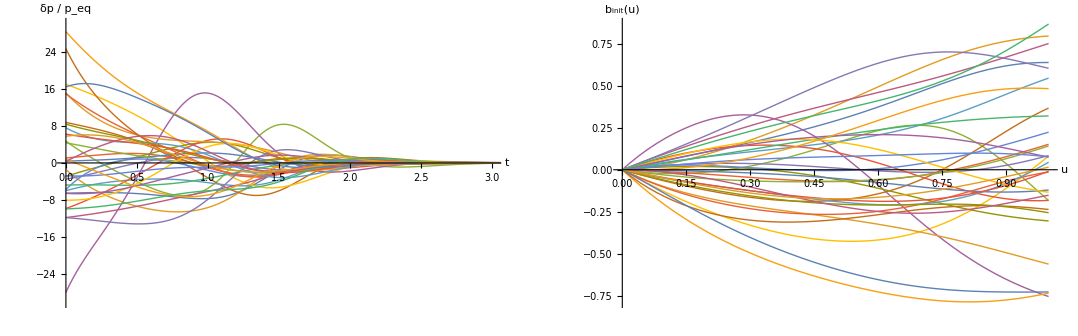

```mathematica
BkgToShow=Table[i,{i,1,NBkgs}];
PressurePlots=ListPlot[Table[δpNorm[bi],{bi,BkgToShow}],Joined->True,AxesLabel->{Style["t",FontSize->18,Bold,Italic],Style["δp / p_eq",FontSize->18,Bold,Italic]},PlotRange->{{0,3},{-30,30}},ImageSize->500,LabelStyle->Directive[Black,14],PlotStyle->Thick];
ICPlots=Plot[Evaluate[Table[bForms[[bi]],{bi,BkgToShow}]],{u,0,1},AxesLabel->{Style["u",FontSize->18,Bold,Italic],Style["b_init(u)",FontSize->18,Bold,Italic]},PlotRange->All,ImageSize->500,LabelStyle->Directive[Black,14],PlotStyle->Thick];
GraphicsGrid[{{PressurePlots,ICPlots}}]
```